```mathematica
"SINGLE CSTR";

Clear[k1,k2,k3,Cao]
Solve[Ca-Cao==t*(-k1*Ca-k3*Ca^2),Ca]
Solve[Cb==t*(Ca-k2*Cb),Cb]
Solve[Cc==t*k2*Cb,Cc]
Solve[Cd==t*Cao*k3*Ca^2,Cd]
```

{{Ca→(-1-k1 t-√(4 Cao k3 t+(1+k1 t)^2))/(2 k3 t)},{Ca→(-1-k1 t+√(4 Cao k3 t+(1+k1 t)^2))/(2 k3 t)}}

{{Cb→(Ca t)/(1+k2 t)}}

{{Cc→Cb k2 t}}

{{Cd→Ca^2 Cao k3 t}}

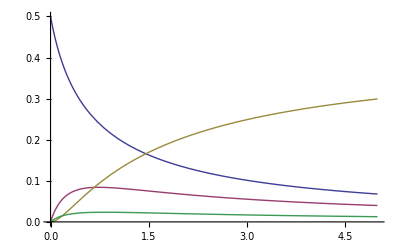

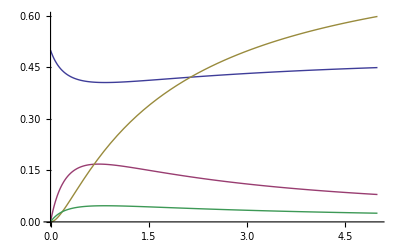

NMaximize::nrnum: The function value 1.728698760420819`  - 4.671772743284529` ⅈ is not a real number at {t} = {-0.5230966103516175`}.

MaxValue[(0.454545 (-1-1.2 t+√(2.2 t+(1+1.2 t)^2)))/(1+1.5 t),t]

```mathematica
k1=1.2;
k2=1.5;
k3=1.1;
Cao=0.5;
CaCSTR[t_]=(-1-k1*t+√(4*Cao*k3*t+(1+k1*t)^2))/(2*k3*t);
CbCSTR[t_]=(t*CaCSTR[t])/(1+k2*t);
CcCSTR[t_]=CbCSTR[t]*k2*t;
CdCSTR[t_]=(CaCSTR[t]^2)*Cao*k3*t;

CaCSTRseries[t_]=t*(k1*CaCSTR[t]-k3*CaCSTR[t]^2)+CaCSTR[t];
CbCSTRseries[t_]=t*(CaCSTR[t]-k2*CbCSTR[t])+CbCSTR[t];
CcCSTRseries[t_]=t*k2*CbCSTR[t]+CcCSTR[t];
CdCSTRseries[t_]=t*Cao*k3*CaCSTR[t]^2+CdCSTR[t];

Plot[{CaCSTR[t],CbCSTR[t],CcCSTR[t], CdCSTR[t]},{t,0,5},PlotRange->All]

Plot[{CaCSTRseries[t],CbCSTRseries[t],CcCSTRseries[t],CdCSTRseries[t]},{t,0,5}, PlotRange->All]

MaxValue[CbCSTR[t],t]
```